```mathematica
Quit[];
```

```mathematica
<<MaTeX`
```

## Modelo de formación de opinión

### Interacción entre individuos con el mismo nivel de confianza

```mathematica
(* Consideramos n individuos.  *)
(* Asignamos números aleatorias entre 0 y 1 a cada individuo, esto le llamaremos opinione *)
(* Los individuos interactuarán N veces,  es decir habrán N interaciones entre los 100 individuos. N = interations  *)
(* Asignamos un nivel de confidencias "δ" el cual determinará si los individuos cambian o no de opinión. Para este caso el nivel de confianza es igual para todos los individuos. *)
(* Definimos un factor de convergencias μ el cual interviene en el cambo de opinión mediante la siguiente ecuación:
Subscript[x, i+1] = Subscript[x, n] + μ(Subscript[x, k] - Subscript[x, i]). *)
```

#### El primer caso a evaluar será con cien individuos con diez mil interacciones entre ellos, un grado de tolerancia 0.5 y un factor de convergencia μ=0.5

```mathematica
n=100; 
opinions=RandomReal[{0,1},n]; 
iterations=10000; 
δ=0.5; 
μ=0.5;
```

```mathematica
(* La siguiente función "updateOpinions" actualiza la opinión de un individuo al azar (Subscript[x, i]) si se cumple la condición |Subscript[x, i]-Subscript[x, k]| < δ.  *)
```

```mathematica
updateOpinions[opinions_List]:=Block[{i,j,opinionDifference,newOpinions=opinions},
i=RandomInteger[{1,n}];
j=RandomInteger[{1,n}];
opinionDifference=Abs[opinions[[i]]-opinions[[j]]];
If[opinionDifference<=δ,newOpinions[[i]]=opinions[[i]]+μ (opinions[[j]]-opinions[[i]]);
newOpinions[[j]]=opinions[[j]]+μ (opinions[[i]]-opinions[[j]]);];
newOpinions]
```

```mathematica
(*Aplicamos la función de actualización diez mil veces a la lista inicial de opiniones de tal forma que obtenemos un nuevo arreglo "opinionsHistory" el cual es una matriz de tamaño 100x10000 que contiene en cada fila los diversos cambios de opinión de los individuos. *)
```

```mathematica
opinionsHistory=NestList[updateOpinions,opinions,iterations];
```

```mathematica
(* Se grafica la evolución de las opiniones (Subscript[x, i]) en función del número de iteraciones (tiempo).  *)
```

```mathematica
ListPlot[Transpose[opinionsHistory],PlotRange->{0,1},PlotStyle->Table[Directive[Black,PointSize[0.006]],{Length[Transpose[opinionsHistory]]}],Frame->True,FrameLabel->{"# de iteraciones","Opinión"}]
```

-Graphics-

```mathematica
(* Histogrma de las opiniones iniciales de los cien individuos. *)
```

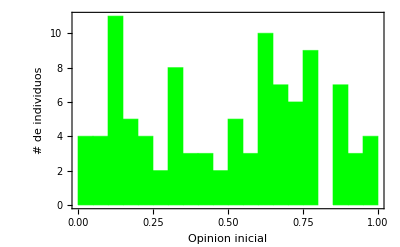

```mathematica
Histogram[opinionsHistory[[1]],20,Frame->True,FrameLabel->{"Opinion inicial","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

```mathematica
(* Histogrma de las opiniones finales de los cien individuos. *)
```

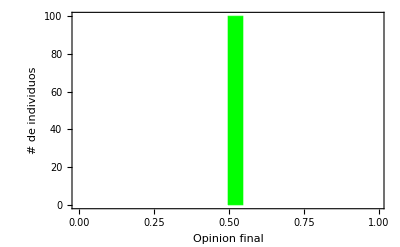

```mathematica
Histogram[opinionsHistory[[-1]],20,Frame->True,FrameLabel->{"Opinion final","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

```mathematica
(* Para el caso δ=μ 1/2 las opiniones convergen al factor de convergencia μ. *)
```

#### Consideremos ahora un caso donde μ=0.5 y δ=0.2 con cien individuos y diez mil interacciones.

```mathematica
n=100; 
opinions=RandomReal[{0,1},n]; 
iterations=10000; 
δ=0.2; 
μ=0.5;
```

```mathematica
(* La siguiente función "updateOpinions" actualiza la opinión de un individuo al azar (Subscript[x, i]) si se cumple la condición |Subscript[x, i]-Subscript[x, k]| < δ.  *)
```

```mathematica
updateOpinions[opinions_List]:=Block[{i,j,opinionDifference,newOpinions=opinions},
i=RandomInteger[{1,n}];
j=RandomInteger[{1,n}];
opinionDifference=Abs[opinions[[i]]-opinions[[j]]];
If[opinionDifference<=δ,newOpinions[[i]]=opinions[[i]]+μ (opinions[[j]]-opinions[[i]]);
newOpinions[[j]]=opinions[[j]]+μ (opinions[[i]]-opinions[[j]]);];
newOpinions]


opinionsHistory=NestList[updateOpinions,opinions,iterations];
```

```mathematica
ListPlot[Transpose[opinionsHistory],PlotRange->{0,1},PlotStyle->Table[Directive[Black,PointSize[0.006]],{Length[Transpose[opinionsHistory]]}],Frame->True,FrameLabel->{"# de iterations","Opinión"}]
```

-Graphics-

```mathematica
(* Histogrma de las opiniones iniciales de los cien individuos. *)
```

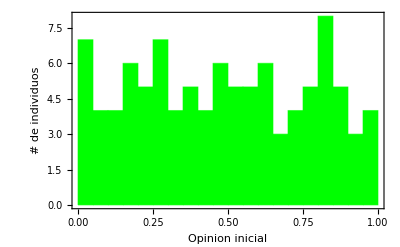

```mathematica
Histogram[opinionsHistory[[1]],20,Frame->True,FrameLabel->{"Opinion inicial","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

```mathematica
(* Histogrma de las opiniones finales de los cien individuos. *)
```

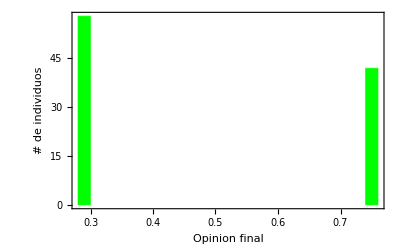

```mathematica
Histogram[opinionsHistory[[-1]],20,Frame->True,FrameLabel->{"Opinion final","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

```mathematica
(*fig_2_3*)
```

```mathematica
(* Para el caso δ=0.2  y μ 1/2 las opiniones tienden a polarizarce principalmente en dos opciones. *)
```

### Interacción entre individuos con diferente nivel de confianza y propaganda

```mathematica
(* Consideramos ahora la influencia de una propaganda "S" sobre la opinión de los individuos. La probabilidad de un individuo interactuar con la propaganda será "m" mientrasa que la probabiliad de interactuar con oro individuo será "1-m". La actualización en la opinión del individuo Subscript[x, i]  por la propagan S será: Subscript[x, n+1]^i = Subscript[x, n]^i + β(S-Subscript[x, n]^i)  *)
```

#### Caso extremo con S = 1, m = 0.1 y μ =β =0.5

```mathematica
n=100; 
opinions=RandomReal[{0,1},n]; 
δ = RandomReal[{0,1},n];
iterations=10000; 
μ=0.5; 
β=0.5;
m =0.1;
S=1;
P[m_]:=RandomVariate[BinomialDistribution[1,m],1][[1]];
```

```mathematica
(* Evaluamos si existe un individuo lider es decir Subscript[δ, k] = 0. *)
```

```mathematica
MemberQ[δ,0]
```

False

```mathematica
updateOpinions[opinions_List]:=Block[{i,j,opinionDifference,newOpinions=opinions},
i=RandomInteger[{1,n}];
j=RandomInteger[{1,n}];
If[P[m]==1,(opinionDifference=Abs[opinions[[i]]-S];
If[opinionDifference<=δ[[i]],newOpinions[[i]]=opinions[[i]]+β(S-opinions[[i]]);];),
(opinionDifference=Abs[opinions[[i]]-opinions[[j]]];
If[opinionDifference<=δ[[i]],newOpinions[[i]]=opinions[[i]]+μ (opinions[[j]]-opinions[[i]]);];
If[opinionDifference<=δ[[j]],newOpinions[[j]]=opinions[[j]]+μ (opinions[[i]]-opinions[[j]]);];)];
newOpinions]
```

```mathematica
opinionsHistory=NestList[updateOpinions,opinions,iterations];
```

```mathematica
ListPlot[Transpose[opinionsHistory],PlotRange->{0,1},PlotStyle->Table[Directive[Black,PointSize[0.006]],{Length[Transpose[opinionsHistory]]}],Frame->True,FrameLabel->{"# de iterations","Opinión"}]
```

-Graphics-

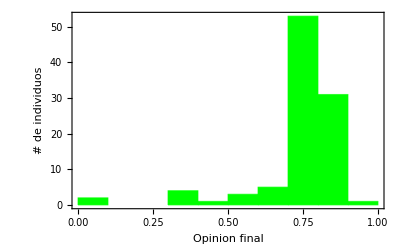

```mathematica
Histogram[opinionsHistory[[-1]],10,Frame->True,FrameLabel->{"Opinion final","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

```mathematica
(* En el caso en que la probabilidad de ser afectada por la propaganda es considerablemente inferior a la probabilidad de interactuar con otro individuo (m=0.1) las opiniones no se aglomeran entonrno a la opinión de la propaganda S=1.   *)
```

#### Introducimos un lider δ_lider = 0

```mathematica
RandomReal[{0,1},1]
```

{0.790829}

```mathematica
n=10; 
opinions={0.518,0.466,0.724,0.092,0.657,0.943,0.304,0.503,0.890,0.240}; 
δ = {0.297,0.399,0.905,0,0.351,0.294,0.227,0.074,0.68,0.790};
iterations=10000; 
μ=0.5; 
β=0.5;
m =0.001;
S=0.5;
P[m_]:=RandomVariate[BinomialDistribution[1,m],1][[1]];
```

```mathematica
(* Evaluamos si existe un individuo lider es decir Subscript[δ, k] = 0 y su posicion en el arreglo. *)
```

```mathematica
MemberQ[δ,0]
```

True

```mathematica
Position[δ,0][[1]][[1]]
```

4

```mathematica
opinions[[Position[δ,0][[1]][[1]]]]
```

0.092

```mathematica
updateOpinions[opinions_List]:=Block[{i,j,opinionDifference,newOpinions=opinions},
i=RandomInteger[{1,n}];
j=RandomInteger[{1,n}];
If[P[m]==1,(opinionDifference=Abs[opinions[[i]]-S];
If[opinionDifference<=δ[[i]],newOpinions[[i]]=opinions[[i]]+β(S-opinions[[i]]);];),
(opinionDifference=Abs[opinions[[i]]-opinions[[j]]];
If[opinionDifference<=δ[[i]],newOpinions[[i]]=opinions[[i]]+μ (opinions[[j]]-opinions[[i]]);];
If[opinionDifference<=δ[[j]],newOpinions[[j]]=opinions[[j]]+μ (opinions[[i]]-opinions[[j]]);];)];
newOpinions]
```

```mathematica
opinionsHistory=NestList[updateOpinions,opinions,iterations];
```

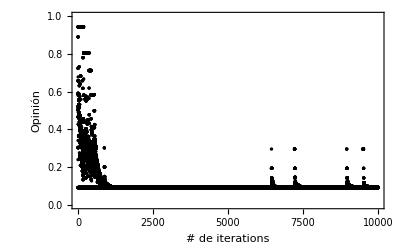

```mathematica
ListPlot[Transpose[opinionsHistory],PlotRange->{0,1},PlotStyle->Table[Directive[Black,PointSize[0.006]],{Length[Transpose[opinionsHistory]]}],Frame->True,FrameLabel->{"# de iterations","Opinión"}]
```

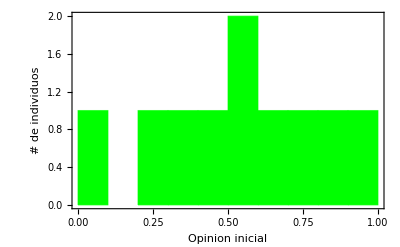

```mathematica
Histogram[opinionsHistory[[1]],10,Frame->True,FrameLabel->{"Opinion inicial","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

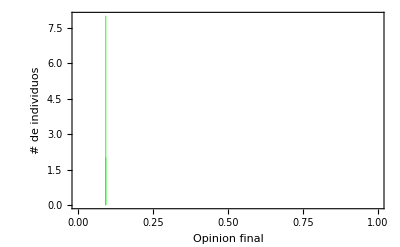

```mathematica
Histogram[opinionsHistory[[-1]],2,Frame->True,PlotRange->{{0,1},All},FrameLabel->{"Opinion final","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

#### Introducimos dos lideres δ_lider = 0

```mathematica
RandomReal[{0,1},1]
```

{0.0861443}

```mathematica
n=17; 
opinions={0.518,0.466,0.724,0.092,0.657,0.943,0.304,0.503,0.618,0.890,0.240,0.263,0.722,0.812,0.536,0.149,0.304}; 
δ = {0.297,0.399,0.905,0,0.351,0.294,0.227,0.074,0,0.68,0.790,0.0710,0.823,0.0109,0.570,0.4008,0.698};
iterations=1000; 
μ=0.5; 
β=0.5;
m =0.2;
S=1.0;
P[m_]:=RandomVariate[BinomialDistribution[1,m],1][[1]];
```

```mathematica
updateOpinions[opinions_List]:=Block[{i,j,opinionDifference,newOpinions=opinions},
i=RandomInteger[{1,n}];
j=RandomInteger[{1,n}];
If[P[m]==1,(opinionDifference=Abs[opinions[[i]]-S];
If[opinionDifference<=δ[[i]],newOpinions[[i]]=opinions[[i]]+β(S-opinions[[i]]);];),
(opinionDifference=Abs[opinions[[i]]-opinions[[j]]];
If[opinionDifference<=δ[[i]],newOpinions[[i]]=opinions[[i]]+μ (opinions[[j]]-opinions[[i]]);];
If[opinionDifference<=δ[[j]],newOpinions[[j]]=opinions[[j]]+μ (opinions[[i]]-opinions[[j]]);];)];
newOpinions]
```

```mathematica
opinionsHistory=NestList[updateOpinions,opinions,iterations];
```

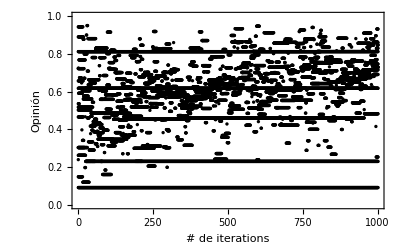

```mathematica
ListPlot[Transpose[opinionsHistory],PlotRange->{0,1},PlotStyle->Table[Directive[Black,PointSize[0.006]],{Length[Transpose[opinionsHistory]]}],Frame->True,FrameLabel->{"# de iterations","Opinión"}]
```

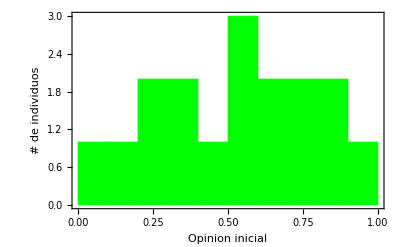

```mathematica
Histogram[opinionsHistory[[1]],10,Frame->True,FrameLabel->{"Opinion inicial","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```

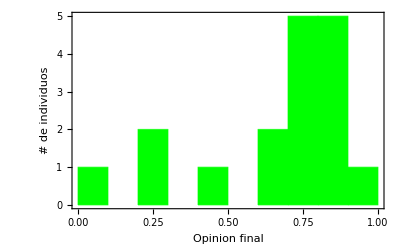

```mathematica
Histogram[opinionsHistory[[-1]],10,Frame->True,PlotRange->{{0,1},All},FrameLabel->{"Opinion final","# de individuos"},ChartStyle->Green,ChartBaseStyle->EdgeForm[Dashed]]
```